```mathematica
(*******IMPORT Data File*********)
Datafile=Import[NotebookDirectory[]<>"output.txt","Table"];
Datafile[[All,4]]=Abs[Datafile[[All,4]]];
```

```mathematica
(****critical temperature*********)
Tc=N[2/Log[1+Sqrt[2]]];
Tc=2.28;
```

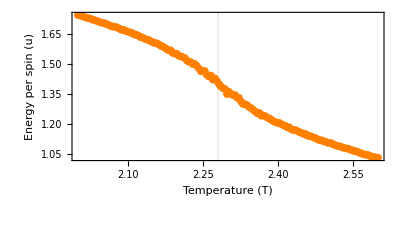

```mathematica
(***Energy***)
Plota=Show[ListPlot[Datafile[[All,{1,2}]],Frame->True,PlotStyle->Orange,PlotRange->Full,FrameLabel->{"Temperature (T)","Energy per spin (u)"},BaseStyle->{FontWeight->"Plain",FontSize->15},GridLines->{{{Tc,{Black,Dashed,Thick}}}}],Graphics[Text[Style["T=T_C",Gray],{Tc-0.05,-1.1}]]]
Export[NotebookDirectory[]<>"Energy.pdf",Plota,"PDF"];
```

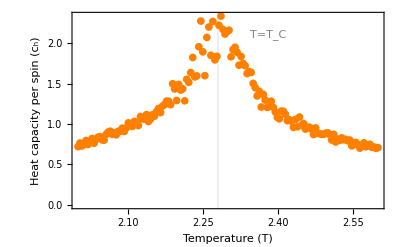

```mathematica
(****Heat Capacity******)
Plotb=Show[ListPlot[Datafile[[All,{1,3}]],Frame->True,PlotStyle->Orange,PlotRange->Full,FrameLabel->{"Temperature (T)","Heat capacity per spin (c_h)"},BaseStyle->{FontWeight->"Plain",FontSize->15},GridLines->{{{Tc,{Black,Dashed,Thick}}},None}],Graphics[Text[Style["T=T_C",Gray],{Tc+0.1,2.1}]]]
Export[NotebookDirectory[]<>"HeatCapacity.pdf",Plotb,"PDF"];
```

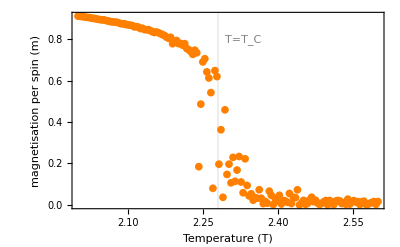

```mathematica
(****Magnetisation*****)
Plotc=Show[ListPlot[Datafile[[All,{1,4}]],Frame->True,PlotStyle->Orange,PlotRange->Full,FrameLabel->{"Temperature (T)","magnetisation per spin (m)"},BaseStyle->{FontWeight->"Plain",FontSize->15},GridLines->{{{Tc,{Black,Dashed,Thick}}},None}],Graphics[Text[Style["T=T_C",Gray],{Tc+0.05,0.8}]]]
Export[NotebookDirectory[]<>"Magnetisation.pdf",Plotc,"PDF"];
```

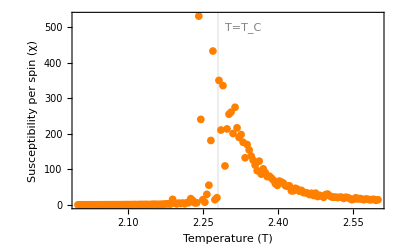

```mathematica
(***Susceptibility**********)
Plotd=Show[ListPlot[Datafile[[All,{1,5}]],Frame->True,PlotStyle->Orange,FrameLabel->{"Temperature (T)","Susceptibility per spin (χ)"},PlotRange->Full,BaseStyle->{FontWeight->"Plain",FontSize->15},GridLines->{{{Tc,{Black,Dashed,Thick}}},None}],Graphics[Text[Style["T=T_C",Gray],{Tc+0.05,500}]]]
Export[NotebookDirectory[]<>"Susceptibility.pdf",Plotd,"PDF"];
```

```mathematica
(***critical indices: transofrmation of the x axis*******)
Datafile2=Datafile;
Datafile2[[All,1]]-=Tc;
TaboveTc=Select[Datafile2,#[[1]]>0&];
TbelowTc=Select[Datafile2,#[[1]]<0&];
TbelowTc[[All,1]]=Abs[TbelowTc[[All,1]]];
```

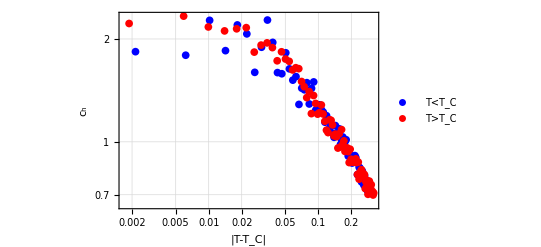

```mathematica
(****critical exponent 1: alpha****)
Plote1=Show[ListLogLogPlot[{TbelowTc[[All,{1,3}]],TaboveTc[[All,{1,3}]]},PlotStyle->{Blue,Red},PlotLegends->{"T<T_C","T>T_C"},GridLines->Automatic],Frame->True,FrameLabel->{"|T-T_C|","c_h"},BaseStyle->{FontWeight->"Plain",FontSize->12}]
Export[NotebookDirectory[]<>"Alpha.pdf",Plote1,"PDF"];
```

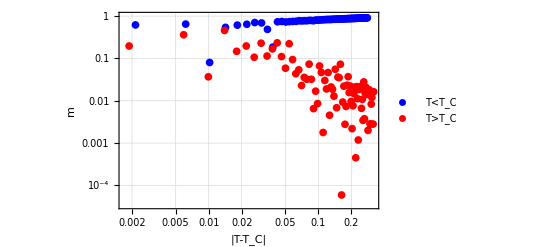

```mathematica
(********Critical behaviour of the magnetisation***)
Plote2=Show[ListLogLogPlot[{TbelowTc[[All,{1,4}]],TaboveTc[[All,{1,4}]]},PlotStyle->{Blue,Red},PlotLegends->{"T<T_C","T>T_C"},GridLines->Automatic],Frame->True,FrameLabel->{"|T-T_C|","m"},BaseStyle->{FontWeight->"Plain",FontSize->12}]
Export[NotebookDirectory[]<>"Beta_1.pdf",Plote2,"PDF"];
```

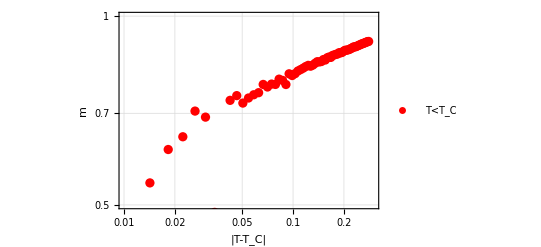

```mathematica
(****critical exponent 2: beta****)
Plote3=Show[ListLogLogPlot[{TbelowTc[[All,{1,4}]]},PlotStyle->{Blue,Red},PlotLegends->{"T<T_C","T>T_C"},GridLines->Automatic,PlotRange->{{0.01,0.3},{0.5,1}}],Frame->True,FrameLabel->{"|T-T_C|","m"},BaseStyle->{FontWeight->"Plain",FontSize->12}]
Export[NotebookDirectory[]<>"Beta_2.pdf",Plote3,"PDF"];
```

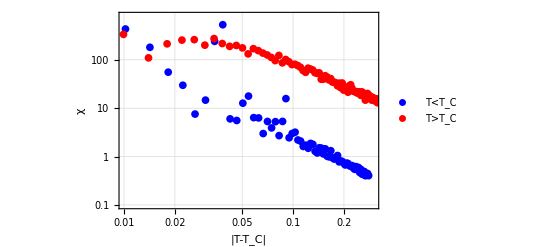

```mathematica
(****critical exponent 3: gamma****)
Plote4=Show[ListLogLogPlot[{TbelowTc[[All,{1,5}]],TaboveTc[[All,{1,5}]]},PlotStyle->{Blue,Red},PlotLegends->{"T<T_C","T>T_C"},GridLines->Automatic,PlotRange->{{0.01,0.3},{0.1,800}}],
Frame->True,FrameLabel->{"|T-T_C|","χ"},BaseStyle->{FontWeight->"Plain",FontSize->12}]
Export[NotebookDirectory[]<>"Gamma.pdf",Plote4,"PDF"];
```